```mathematica
data = Import["/Users/guillemontanari/C3/Datos/Ind_Sit_Jur.csv", "CSV"];
```

```mathematica
Length[data]
```

101

```mathematica
PositionIndex[data[[1]]]
```

<|CLAVE DE ENTIDAD→{1},ENTIDAD→{2},CENTRO DE REINSERCIÓN SOCIAL→{3},SENTENCIADO→{4},PROCESADO→{5},→{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72}|>

```mathematica
ndata =data[[All, 1;;5]];

ndata
```

{{CLAVE DE ENTIDAD,ENTIDAD,CENTRO DE REINSERCIÓN SOCIAL,SENTENCIADO,PROCESADO},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #4 ""CUICATLÁN"".,5,3},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #8 ""MATÍAS ROMERO"".,0,4},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #1 ""PENITENCIARIA CENTRAL"".,24,12},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #9 ""JUCHITÁN"".,0,2},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #6 ""TUXTEPEC"".,4,1},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #5 ""COSOLAPA"".,0,2},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #2 ""ETLA"".,2,7},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #3 ""MIAHUATLÁN"".,4,4},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #13 ""HUAJUAPAN"".,2,0},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL FEMENIL ""TANIVET"".,4,10},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #7 ""TEHUANTEPEC"".,14,42},{20,OAXACA,CENTRO FEDERAL DE READAPTACIÓN SOCIAL #13 ""OAXACA"".,28,15},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #10 ""JUQUILA"".,1,0},{7,CHIAPAS,CENTRO ESTATAL DE REINSERCIÓN SOCIAL PARA SENTENCIADOS # 14 ""EL AMATE"".,46,105},{7,CHIAPAS,CENTRO ESTATAL DE REINSERCIÓN SOCIAL PARA SENTENCIADOS # 5.,9,12},{7,CHIAPAS,CENTRO ESTATAL DE REINSERCIÓN SOCIAL PARA SENTENCIADOS # 17 ""EL BAMBÚ"".,5,1},{7,CHIAPAS,CENTRO ESTATAL DE REINSERCIÓN SOCIAL PARA SENTENCIADOS # 4 ""TAPACHULA"".,0,4},{7,CHIAPAS,CENTRO ESTATAL DE REINSERCIÓN SOCIAL PARA SENTENCIADOS # 164 ""OCOSINGO"".,0,3},{18,NAYARIT,CENTRO FEDERAL DE READAPTACIÓN SOCIAL # 4 ""NOROESTE"",11,11},{18,NAYARIT,COMPLEJO PENITENCIARIO ISLAS MARÍAS,39,0},{18,NAYARIT,CENTRO DE REHABILITACIÓN SOCIAL VENUSTIANO CARRANZA,10,7},{26,SONORA,CENTRO DE REINSERCIÓN SOCIAL ""CD. OBREGÓN"". ,0,1},{26,SONORA,CENTRO DE REINSERCIÓN SOCIAL ""NAVOJOA"". ,0,2},{26,SONORA,CENTRO DE REINSERCIÓN SOCIAL ""NOGALES II VARONIL"".,8,6},{26,SONORA,CENTRO FEDERAL DE READAPTACIÓN SOCIAL #11 ""CPS-SONORA"". ,5,15},{26,SONORA,CENTRO DE REINSERCIÓN SOCIAL ""HERMOSILLO"". ,2,35},{12,GUERRERO,CENTRO DE REINSERCIÓN SOCIAL ""ACAPULCO DE JUÁREZ"".,11,10},{12,GUERRERO,CENTRO DE REINSERCIÓN SOCIAL ""CHILPANCINGO DE LOS BRAVOS"". ,2,17},{12,GUERRERO,CENTRO DE REINSERCIÓN SOCIAL ""IGUALA DE LA INDEPENDENCIA"".,0,1},{9,DISTRITO FEDERAL,RECLUSORIO PREVENTIVO VARONIL NORTE.,3,0},{9,DISTRITO FEDERAL,RECLUSORIO PREVENTIVO VARONIL SUR.,9,0},{9,DISTRITO FEDERAL,RECLUSORIO PREVENTIVO VARONIL ORIENTE.,10,6},{9,DISTRITO FEDERAL,PENITENCIARIA DISTRITO FEDERAL.,5,0},{9,DISTRITO FEDERAL,RECLUSORIO FEMENIL SANTA MARTHA ACATITLA.,0,1},{9,DISTRITO FEDERAL,CENTRO FEMENIL DE READAPTACIÓN SOCIAL TEPEPAN.,0,1},{8,CHIHUAHUA,CENTRO DE REINSERCIÓN SOCIAL ESTATAL, # 1.,2,2},{8,CHIHUAHUA,CENTRO DE REINSERCIÓN SOCIAL ESTATAL, # 2.,1,0},{8,CHIHUAHUA,CENTRO DE REINSERCIÓN SOCIAL ESTATAL, # 3.,3,0},{8,CHIHUAHUA,CENTRO DE REINSERCIÓN SOCIAL ESTATAL, # 4.,1,0},{8,CHIHUAHUA,CENTRO DE REINSERCIÓN SOCIAL DISTRITAL, ""GUACHOCHI"".,4,0},{8,CHIHUAHUA,CENTRO DE REINSERCIÓN SOCIAL DISTRITAL, ""GUERRERO"".,3,0},{8,CHIHUAHUA,CENTRO DE REINSERCIÓN SOCIAL DISTRITAL, ""GUADALUPE Y CALVO"".,0,2},{8,CHIHUAHUA,CENTRO DE REINSERCIÓN SOCIAL DE BAJO RIESGO.,1,1},{8,CHIHUAHUA,CENTRO FEDERAL DE READAPTACIÓN SOCIAL # 9 ""NORTE"".,9,3},{31,YUCATÁN,CENTRO DE REINSERCIÓN SOCIAL VARONIL DE MÉRIDA.,19,5},{31,YUCATÁN,CENTRO DE REINSERCIÓN SOCIAL FEMENIL DE MÉRIDA.,2,0},{31,YUCATÁN,CENTRO DE REINSERCIÓN SOCIAL DE EBTUM VALLADOLID.,1,0},{31,YUCATÁN,CENTRO DE REINSERCIÓN SOCIAL EN TEKAX.,1,0},{15,ESTADO DE MÉXICO,CENTRO DE PREVENSIÓN Y READAPTACIÓN SOCIAL DE SANTIAGUITO VARONIL,1,6},{15,ESTADO DE MÉXICO,CENTRO DE PREVENSIÓN Y READPTACIÓN SOCIAL DE SANTIAGUITO FEMENIL,1,0},{15,ESTADO DE MÉXICO,CENTRO DE PREVENSIÓN Y READAPTACIÓN SOCIAL DE OTUMBA ""TEPACHICO"",1,0},{15,ESTADO DE MÉXICO,CENTRO DE PREVENSIÓN Y READAPTACIÓN SOCIAL DE VALLE DE BRAVO,1,0},{15,ESTADO DE MÉXICO,CENTRO DE PREVENCIÓN Y READAPTACIÓN SOCIAL NEZA VARONIL ""BORDO"",1,0},{15,ESTADO DE MÉXICO,CENTRO DE PREVENCIÓN DE READAPTACIÓN SOCIAL NEZA FEMENIL ""BORDO"",0,1},{15,ESTADO DE MÉXICO,CENTRO FEDERAL DE READAPTACIÓN SOCIAL  N° 1 ""ALTIPLANO"",0,8},{15,ESTADO DE MÉXICO,CENTRO DE PREVENSIÓN Y READAPTACIÓN SOCIAL  DE TLANEPANTLA ""BARRIENTOS"",0,2},{13,HIDALGO,CENTRO DE REINSERCIÓN SOCIAL DE PACHUCA,6,9},{13,HIDALGO,CENTRO DE REINSERCIÓN SOCIAL DE IXMIQUILPAN,1,0},{13,HIDALGO,CENTRO DE REINSERCIÓN SOCIAL DE ACTOPAN,0,2},{25,SINALOA,CENTRO DE EJECUCIÓN DE LAS CONSECUENCIAS JURÍDICAS DEL DELITO, LOS MOCHIS. ,7,4},{25,SINALOA,CENTRO DE EJECUCIÓN DE LAS CONSECUENCIAS JURÍDICAS DEL DELITO, MAZATLÁN. ,0,4},{25,SINALOA,CENTRO FEDERAL DE READAPTACIÓN SOCIAL # 8 ""NOR-PONIENTE"".,2,0},{16,MICHOACÁN,CENTRO DE REINSERCIÓN SOCIAL ""LIC. DAVID FRANCO RODRÍGUEZ"" MIL CUMBRES CHARO. ,3,0},{16,MICHOACÁN,CENTRO DE REINSERCIÓN SOCIAL ""GRAL. FRANCISCO J. MUJICA"" MORELIA. ,2,3},{16,MICHOACÁN,CENTRO DE REINSERCIÓN SOCIAL ""LIC. EDUARDO RUÍZ"" URUAPAN. ,4,1},{16,MICHOACÁN,CENTRO DE REINSERCIÓN SOCIAL LA PIEDAD. ,1,0},{16,MICHOACÁN,CENTRO DE REINSERCIÓN SOCIAL ZAMORA ,0,2},{21,PUEBLA,CENTRO DE REINSERCIÓN SOCIAL ""PUEBLA"". ,2,2},{21,PUEBLA,CENTRO DE REINSERCIÓN SOCIAL ""HUAUCHINANGO"".,4,3},{21,PUEBLA,CENTRO DE REINSERCIÓN SOCIAL ""CHOLULA"". ,1,0},{21,PUEBLA,CENTRO DE REINSERCIÓN SOCIAL ""TEHUACÁN"". ,3,0},{2,BAJA CALIFORNIA,CENTRO DE REINSERCIÓN SOCIAL ""MEXICALI"".,0,3},{2,BAJA CALIFORNIA,CENTRO DE REINSERCIÓN SOCIAL ""ENSENADA"".,7,3},{2,BAJA CALIFORNIA,CENTRO DE REINSERCIÓN SOCIAL ""EL HONGO"".,1,0},{30,VERACRUZ,CENTRO DE REINSERCIÓN SOCIAL ""AMATLÁN DE LOS REYES"". ,1,0},{30,VERACRUZ,CENTRO DE REINSERCIÓN SOCIAL ""TUXPAN"".,1,0},{30,VERACRUZ,CENTRO FEDERAL DE READAPTACIÓN SOCIAL #5 ""ORIENTE"". ,2,8},{11,GUANAJUATO,CENTRO FEDERAL DE READAPTACIÓN SOCIAL #12 ""CPS-GUANAJUATO"".,10,1},{6,COLIMA,CENTRO DE REINSERCIÓN SOCIAL ""COLIMA"".,2,9},{17,MORELOS,CENTRO DE READAPTACIÓN SOCIAL DE  MORELOS VARONIL,0,7},{17,MORELOS,CENTRO DE READAPTACIÓN SOCIAL MORELOS FEMENIL,1,0},{17,MORELOS,CARCEL DISTRITAL DE CUAUTLA,2,0},{14,JALISCO,CENTRO DE REINSERCIÓN SOCIAL ""PUENTE GRANDE"". ,0,8},{14,JALISCO,CENTRO FEDERAL DE READAPTACIÓN SOCIAL # 2 ""OCCIDENTE"".,1,1},{27,TABASCO,CENTRO DE REINSERCIÓN SOCIAL ""VILLAHERMOSA"".,1,2},{27,TABASCO,CENTRO FEDERAL DE READAPTACIÓN SOCIAL # 6 ""SURESTE"".,7,0},{10,DURANGO,CENTRO DE REINSERCIÓN SOCIAL  N°1 ""DURANGO"".,1,1},{10,DURANGO,CENTRO FEDERAL DE READAPTACIÓN SOCIAL # 7 ""NOR-NOROESTE."",3,2},{10,DURANGO,CENTRO FEDERAL DE READAPTACIÓN SOCIAL #14 ""CPS-DURANGO"". ,1,0},{4,CAMPECHE,CENTRO DE REINSERCIÓN SOCIAL ""SAN FRANCISCO KOBEN"".,0,7},{5,COAHUILA,CENTRO FEDERAL DE READAPTACIÓN SOCIAL # 10 NOR-NORESTE"".,6,0},{22,QUERÉTARO,CENTRO DE READAPTACIÓN SOCIAL ""SAN JOSÉ EL ALTO"".,1,2},{19,NUEVO LEÓN,CENTRO DE REINSERCIÓN SOCIAL ""CADEREYTA"", NUEVO LEÓN. ,1,0},{23,QUINTANA ROO,CÁRCEL PÚBLICA ""BENITO JUÁREZ"".,0,1},{32,ZACATECAS,CENTRO DE REINSERCIÓN SOCIAL ""CIENEGUILLAS"". ,0,1},{1,AGUASCALIENTES,NO CUENTA CON PERSONAS INDÍGENAS INTERNAS ,0,0},{3,BAJA CALIFORNIA SUR,NO CUENTA CON PERSONAS INDÍGENAS INTERNAS ,0,0},{24,SAN LUIS POTOSÍ,NO CUENTA CON PERSONAS INDÍGENAS INTERNAS ,0,0},{28,TAMAULIPAS,NO CUENTA CON PERSONAS INDÍGENAS INTERNAS ,0,0},{29,TLAXCALA,NO CUENTA CON PERSONAS INDÍGENAS INTERNAS ,0,0}}

```mathematica
data2 = Select[ndata,# [[1]] === 20 &]
```

{{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #4 ""CUICATLÁN"".,5,3},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #8 ""MATÍAS ROMERO"".,0,4},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #1 ""PENITENCIARIA CENTRAL"".,24,12},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #9 ""JUCHITÁN"".,0,2},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #6 ""TUXTEPEC"".,4,1},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #5 ""COSOLAPA"".,0,2},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #2 ""ETLA"".,2,7},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #3 ""MIAHUATLÁN"".,4,4},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #13 ""HUAJUAPAN"".,2,0},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL FEMENIL ""TANIVET"".,4,10},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #7 ""TEHUANTEPEC"".,14,42},{20,OAXACA,CENTRO FEDERAL DE READAPTACIÓN SOCIAL #13 ""OAXACA"".,28,15},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #10 ""JUQUILA"".,1,0}}

```mathematica
data2[[All,{2,4,5}]]
```

{{OAXACA,5,3},{OAXACA,0,4},{OAXACA,24,12},{OAXACA,0,2},{OAXACA,4,1},{OAXACA,0,2},{OAXACA,2,7},{OAXACA,4,4},{OAXACA,2,0},{OAXACA,4,10},{OAXACA,14,42},{OAXACA,28,15},{OAXACA,1,0}}

```mathematica
Total[data2[[All,{4,5}]]]
```

{88,102}

```mathematica
Tally[ndata[[All,{2,4,5}]]]
```

{{{ENTIDAD,SENTENCIADO,PROCESADO},1},{{OAXACA,5,3},1},{{OAXACA,0,4},1},{{OAXACA,24,12},1},{{OAXACA,0,2},2},{{OAXACA,4,1},1},{{OAXACA,2,7},1},{{OAXACA,4,4},1},{{OAXACA,2,0},1},{{OAXACA,4,10},1},{{OAXACA,14,42},1},{{OAXACA,28,15},1},{{OAXACA,1,0},1},{{CHIAPAS,46,105},1},{{CHIAPAS,9,12},1},{{CHIAPAS,5,1},1},{{CHIAPAS,0,4},1},{{CHIAPAS,0,3},1},{{NAYARIT,11,11},1},{{NAYARIT,39,0},1},{{NAYARIT,10,7},1},{{SONORA,0,1},1},{{SONORA,0,2},1},{{SONORA,8,6},1},{{SONORA,5,15},1},{{SONORA,2,35},1},{{GUERRERO,11,10},1},{{GUERRERO,2,17},1},{{GUERRERO,0,1},1},{{DISTRITO FEDERAL,3,0},1},{{DISTRITO FEDERAL,9,0},1},{{DISTRITO FEDERAL,10,6},1},{{DISTRITO FEDERAL,5,0},1},{{DISTRITO FEDERAL,0,1},2},{{CHIHUAHUA,2,2},1},{{CHIHUAHUA,1,0},2},{{CHIHUAHUA,3,0},2},{{CHIHUAHUA,4,0},1},{{CHIHUAHUA,0,2},1},{{CHIHUAHUA,1,1},1},{{CHIHUAHUA,9,3},1},{{YUCATÁN,19,5},1},{{YUCATÁN,2,0},1},{{YUCATÁN,1,0},2},{{ESTADO DE MÉXICO,1,6},1},{{ESTADO DE MÉXICO,1,0},4},{{ESTADO DE MÉXICO,0,1},1},{{ESTADO DE MÉXICO,0,8},1},{{ESTADO DE MÉXICO,0,2},1},{{HIDALGO,6,9},1},{{HIDALGO,1,0},1},{{HIDALGO,0,2},1},{{SINALOA,7,4},1},{{SINALOA,0,4},1},{{SINALOA,2,0},1},{{MICHOACÁN,3,0},1},{{MICHOACÁN,2,3},1},{{MICHOACÁN,4,1},1},{{MICHOACÁN,1,0},1},{{MICHOACÁN,0,2},1},{{PUEBLA,2,2},1},{{PUEBLA,4,3},1},{{PUEBLA,1,0},1},{{PUEBLA,3,0},1},{{BAJA CALIFORNIA,0,3},1},{{BAJA CALIFORNIA,7,3},1},{{BAJA CALIFORNIA,1,0},1},{{VERACRUZ,1,0},2},{{VERACRUZ,2,8},1},{{GUANAJUATO,10,1},1},{{COLIMA,2,9},1},{{MORELOS,0,7},1},{{MORELOS,1,0},1},{{MORELOS,2,0},1},{{JALISCO,0,8},1},{{JALISCO,1,1},1},{{TABASCO,1,2},1},{{TABASCO,7,0},1},{{DURANGO,1,1},1},{{DURANGO,3,2},1},{{DURANGO,1,0},1},{{CAMPECHE,0,7},1},{{COAHUILA,6,0},1},{{QUERÉTARO,1,2},1},{{NUEVO LEÓN,1,0},1},{{QUINTANA ROO,0,1},1},{{ZACATECAS,0,1},1},{{AGUASCALIENTES,0,0},1},{{BAJA CALIFORNIA SUR,0,0},1},{{SAN LUIS POTOSÍ,0,0},1},{{TAMAULIPAS,0,0},1},{{TLAXCALA,0,0},1}}

```mathematica
TableForm[ndata];
```

```mathematica
Select[ndata,#[[1]] === 20 ∨#[[1]] ===32 &]
```

{{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #4 ""CUICATLÁN"".,5,3},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #8 ""MATÍAS ROMERO"".,0,4},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #1 ""PENITENCIARIA CENTRAL"".,24,12},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #9 ""JUCHITÁN"".,0,2},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #6 ""TUXTEPEC"".,4,1},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #5 ""COSOLAPA"".,0,2},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #2 ""ETLA"".,2,7},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #3 ""MIAHUATLÁN"".,4,4},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #13 ""HUAJUAPAN"".,2,0},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL FEMENIL ""TANIVET"".,4,10},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #7 ""TEHUANTEPEC"".,14,42},{20,OAXACA,CENTRO FEDERAL DE READAPTACIÓN SOCIAL #13 ""OAXACA"".,28,15},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #10 ""JUQUILA"".,1,0},{32,ZACATECAS,CENTRO DE REINSERCIÓN SOCIAL ""CIENEGUILLAS"". ,0,1}}

```mathematica
sdata= Select[ndata,#[[1]] === 20&];
```

```mathematica
Total[sdata[[All,4]]]
```

88

```mathematica
Sentenciados[data_, estado_] := Block[{sdata1, sdata2},
sdata1=Select[data,#[[2]] === estado &];
sdata2 = sdata1[[All,4]];
Total[sdata2]]
```

```mathematica
Sentenciados[ndata, "OAXACA"]
```

88

```mathematica
88
tdata= DeleteDuplicates[ndata[[2;;-1,2]]]
```

88

{OAXACA,CHIAPAS,NAYARIT,SONORA,GUERRERO,DISTRITO FEDERAL,CHIHUAHUA,YUCATÁN,ESTADO DE MÉXICO,HIDALGO,SINALOA,MICHOACÁN,PUEBLA,BAJA CALIFORNIA,VERACRUZ,GUANAJUATO,COLIMA,MORELOS,JALISCO,TABASCO,DURANGO,CAMPECHE,COAHUILA,QUERÉTARO,NUEVO LEÓN,QUINTANA ROO,ZACATECAS,AGUASCALIENTES,BAJA CALIFORNIA SUR,SAN LUIS POTOSÍ,TAMAULIPAS,TLAXCALA}

```mathematica
Do[
rdata = Sentenciados[ndata,i];
Print[{i,rdata}];
,{i, tdata}];
```

{OAXACA,88}

{CHIAPAS,60}

{NAYARIT,60}

{SONORA,15}

{GUERRERO,13}

{DISTRITO FEDERAL,27}

{CHIHUAHUA,24}

{YUCATÁN,23}

{ESTADO DE MÉXICO,5}

{HIDALGO,7}

{SINALOA,9}

{MICHOACÁN,10}

{PUEBLA,10}

{BAJA CALIFORNIA,8}

{VERACRUZ,4}

{GUANAJUATO,10}

{COLIMA,2}

{MORELOS,3}

{JALISCO,1}

{TABASCO,8}

{DURANGO,5}

{CAMPECHE,0}

{COAHUILA,6}

{QUERÉTARO,1}

{NUEVO LEÓN,1}

{QUINTANA ROO,0}

{ZACATECAS,0}

{AGUASCALIENTES,0}

{BAJA CALIFORNIA SUR,0}

{SAN LUIS POTOSÍ,0}

{TAMAULIPAS,0}

{TLAXCALA,0}

```mathematica
final = {};
Do[
rdata = Sentenciados[ndata,i];
AppendTo[final,{i,rdata}];
,{i, tdata}];
```

```mathematica
final
```

{{OAXACA,88},{CHIAPAS,60},{NAYARIT,60},{SONORA,15},{GUERRERO,13},{DISTRITO FEDERAL,27},{CHIHUAHUA,24},{YUCATÁN,23},{ESTADO DE MÉXICO,5},{HIDALGO,7},{SINALOA,9},{MICHOACÁN,10},{PUEBLA,10},{BAJA CALIFORNIA,8},{VERACRUZ,4},{GUANAJUATO,10},{COLIMA,2},{MORELOS,3},{JALISCO,1},{TABASCO,8},{DURANGO,5},{CAMPECHE,0},{COAHUILA,6},{QUERÉTARO,1},{NUEVO LEÓN,1},{QUINTANA ROO,0},{ZACATECAS,0},{AGUASCALIENTES,0},{BAJA CALIFORNIA SUR,0},{SAN LUIS POTOSÍ,0},{TAMAULIPAS,0},{TLAXCALA,0}}

```mathematica
mdata = Map[Sentenciados[ndata,#]&,tdata]
```

{88,60,60,15,13,27,24,23,5,7,9,10,10,8,4,10,2,3,1,8,5,0,6,1,1,0,0,0,0,0,0,0}

```mathematica
AbsoluteTiming[ Map[Sentenciados[ndata,#]&,tdata]]
```

{0.0037,{88,60,60,15,13,27,24,23,5,7,9,10,10,8,4,10,2,3,1,8,5,0,6,1,1,0,0,0,0,0,0,0}}

```mathematica
Transpose[{tdata, mdata}]
```

{{OAXACA,88},{CHIAPAS,60},{NAYARIT,60},{SONORA,15},{GUERRERO,13},{DISTRITO FEDERAL,27},{CHIHUAHUA,24},{YUCATÁN,23},{ESTADO DE MÉXICO,5},{HIDALGO,7},{SINALOA,9},{MICHOACÁN,10},{PUEBLA,10},{BAJA CALIFORNIA,8},{VERACRUZ,4},{GUANAJUATO,10},{COLIMA,2},{MORELOS,3},{JALISCO,1},{TABASCO,8},{DURANGO,5},{CAMPECHE,0},{COAHUILA,6},{QUERÉTARO,1},{NUEVO LEÓN,1},{QUINTANA ROO,0},{ZACATECAS,0},{AGUASCALIENTES,0},{BAJA CALIFORNIA SUR,0},{SAN LUIS POTOSÍ,0},{TAMAULIPAS,0},{TLAXCALA,0}}

```mathematica
mdata = Map[{#, Sentenciados[ndata,#]}&,tdata]
```

{{OAXACA,88},{CHIAPAS,60},{NAYARIT,60},{SONORA,15},{GUERRERO,13},{DISTRITO FEDERAL,27},{CHIHUAHUA,24},{YUCATÁN,23},{ESTADO DE MÉXICO,5},{HIDALGO,7},{SINALOA,9},{MICHOACÁN,10},{PUEBLA,10},{BAJA CALIFORNIA,8},{VERACRUZ,4},{GUANAJUATO,10},{COLIMA,2},{MORELOS,3},{JALISCO,1},{TABASCO,8},{DURANGO,5},{CAMPECHE,0},{COAHUILA,6},{QUERÉTARO,1},{NUEVO LEÓN,1},{QUINTANA ROO,0},{ZACATECAS,0},{AGUASCALIENTES,0},{BAJA CALIFORNIA SUR,0},{SAN LUIS POTOSÍ,0},{TAMAULIPAS,0},{TLAXCALA,0}}

```mathematica
Export["Desktop/sentenciados.csv", mdata,"CSV"]
```

Desktop/sentenciados.csv

```mathematica
(* 5 FEB 2017  GRAFICAS *)
```

```mathematica
c1 = Circle[{1,1},3]
```

Circle[{1,1},3]

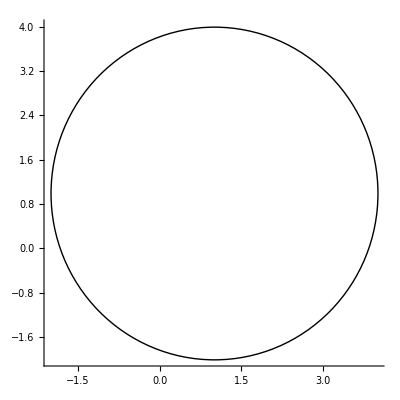

```mathematica
Graphics[c1, Axes -> True]
```

```mathematica
d1 = Disk[{1,1},2]
```

Disk[{1,1},2]



```mathematica
Graphics[d1]
```

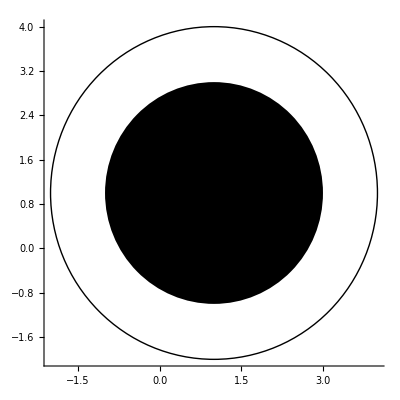

```mathematica
g1 = Graphics[{c1,d1}, Axes -> True]
```

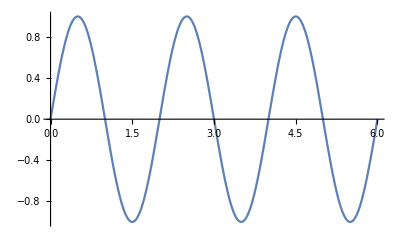

```mathematica
g2 = Plot[Sin[π x], {x,0,6}]
```

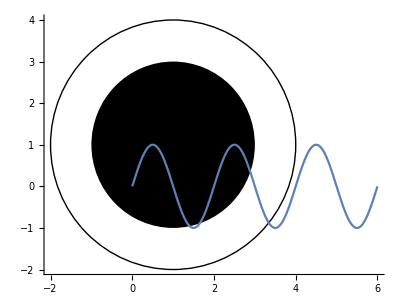

```mathematica
Show[{g1, g2}]
```

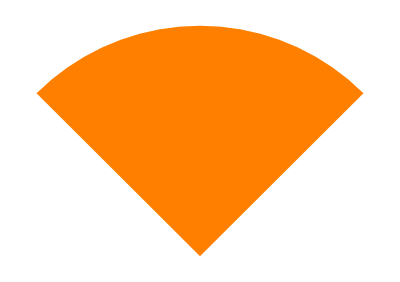

```mathematica
Graphics[{Orange,Disk[{0,0},1,{Pi/4,3Pi/4}]}]
```

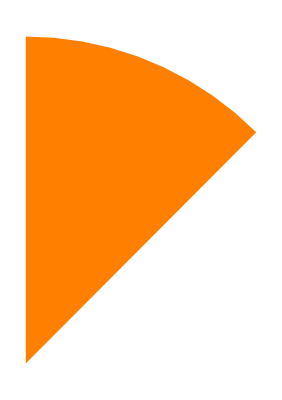

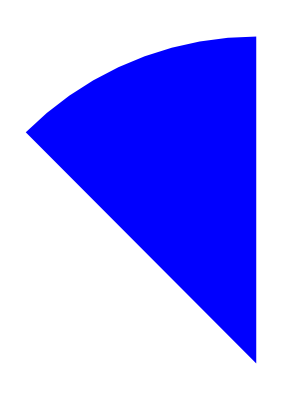

```mathematica
d3 = Graphics[{Orange,Disk[{0,0},1,{Pi/4,Pi/2}]}]
d4 = Graphics[{Blue,Disk[{0,0},1,{Pi/2,3Pi/4}]}]
```

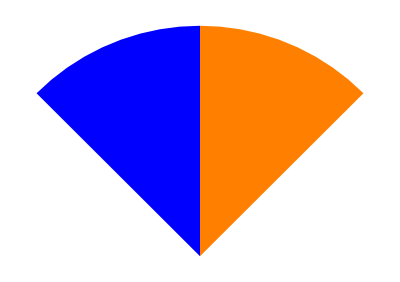

```mathematica
Show[{d3,d4}]
```

```mathematica
RGBColor[1,0,0]
```

-Graphics-

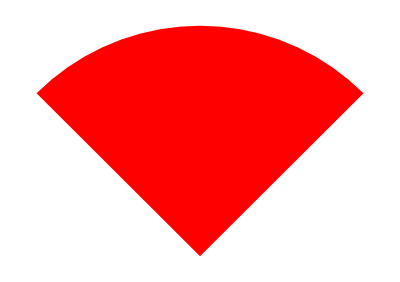

```mathematica
-Graphics-
Graphics[{RGBColor[1,0,0],Disk[{0,0},1,{Pi/4,3Pi/4}]}]
```

```mathematica
r1 = {Yellow, Rectangle[{0,0},{2,2}]}
```

{-Graphics-,Rectangle[{0,0},{2,2}]}

```mathematica
Graphics[{Rotate[r1,π/4], Text[Style["Rect", FontSize->20]]}]
```

-Graphics-

```mathematica
(* Para todos los estados *)
(* Función que toma los estados y me devuelve la suma de sentenciados y procesados por estado *)
```

```mathematica
ndata[[2;;3]]
```

{{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #4 ""CUICATLÁN"".,5,3},{20,OAXACA,CENTRO DE REINSERCIÓN SOCIAL #8 ""MATÍAS ROMERO"".,0,4}}

```mathematica
Sentenciados[data_, estado1_] := Block[{sdata1, sdata2, sdata3},
sdata1=Select[data,#[[2]] === estado1 &];
sdata2 = sdata1[[All,4]];
sdata3 = sdata1[[All,5]];
{estado1,Total[sdata2],Total[sdata3]}]
```

```mathematica
tdata= DeleteDuplicates[ndata[[2;;-1,2]]]
```

{OAXACA,CHIAPAS,NAYARIT,SONORA,GUERRERO,DISTRITO FEDERAL,CHIHUAHUA,YUCATÁN,ESTADO DE MÉXICO,HIDALGO,SINALOA,MICHOACÁN,PUEBLA,BAJA CALIFORNIA,VERACRUZ,GUANAJUATO,COLIMA,MORELOS,JALISCO,TABASCO,DURANGO,CAMPECHE,COAHUILA,QUERÉTARO,NUEVO LEÓN,QUINTANA ROO,ZACATECAS,AGUASCALIENTES,BAJA CALIFORNIA SUR,SAN LUIS POTOSÍ,TAMAULIPAS,TLAXCALA}

```mathematica
Do[
rdata = Sentenciados[ndata,i];
Print[rdata];
,{i, tdata}];
```

{OAXACA,88,102}

{CHIAPAS,60,125}

{NAYARIT,60,18}

{SONORA,15,59}

{GUERRERO,13,28}

{DISTRITO FEDERAL,27,8}

{CHIHUAHUA,24,8}

{YUCATÁN,23,5}

{ESTADO DE MÉXICO,5,17}

{HIDALGO,7,11}

{SINALOA,9,8}

{MICHOACÁN,10,6}

{PUEBLA,10,5}

{BAJA CALIFORNIA,8,6}

{VERACRUZ,4,8}

{GUANAJUATO,10,1}

{COLIMA,2,9}

{MORELOS,3,7}

{JALISCO,1,9}

{TABASCO,8,2}

{DURANGO,5,3}

{CAMPECHE,0,7}

{COAHUILA,6,0}

{QUERÉTARO,1,2}

{NUEVO LEÓN,1,0}

{QUINTANA ROO,0,1}

{ZACATECAS,0,1}

{AGUASCALIENTES,0,0}

{BAJA CALIFORNIA SUR,0,0}

{SAN LUIS POTOSÍ,0,0}

{TAMAULIPAS,0,0}

{TLAXCALA,0,0}

```mathematica
mdata = Map[Sentenciados[ndata,#]&,tdata]
```

{{OAXACA,88,102},{CHIAPAS,60,125},{NAYARIT,60,18},{SONORA,15,59},{GUERRERO,13,28},{DISTRITO FEDERAL,27,8},{CHIHUAHUA,24,8},{YUCATÁN,23,5},{ESTADO DE MÉXICO,5,17},{HIDALGO,7,11},{SINALOA,9,8},{MICHOACÁN,10,6},{PUEBLA,10,5},{BAJA CALIFORNIA,8,6},{VERACRUZ,4,8},{GUANAJUATO,10,1},{COLIMA,2,9},{MORELOS,3,7},{JALISCO,1,9},{TABASCO,8,2},{DURANGO,5,3},{CAMPECHE,0,7},{COAHUILA,6,0},{QUERÉTARO,1,2},{NUEVO LEÓN,1,0},{QUINTANA ROO,0,1},{ZACATECAS,0,1},{AGUASCALIENTES,0,0},{BAJA CALIFORNIA SUR,0,0},{SAN LUIS POTOSÍ,0,0},{TAMAULIPAS,0,0},{TLAXCALA,0,0}}

```mathematica
PrependTo[mdata,{"Estado","Procesados", "Sentenciados"}]
```

{{Estado,Procesados,Sentenciados},{OAXACA,88,102},{CHIAPAS,60,125},{NAYARIT,60,18},{SONORA,15,59},{GUERRERO,13,28},{DISTRITO FEDERAL,27,8},{CHIHUAHUA,24,8},{YUCATÁN,23,5},{ESTADO DE MÉXICO,5,17},{HIDALGO,7,11},{SINALOA,9,8},{MICHOACÁN,10,6},{PUEBLA,10,5},{BAJA CALIFORNIA,8,6},{VERACRUZ,4,8},{GUANAJUATO,10,1},{COLIMA,2,9},{MORELOS,3,7},{JALISCO,1,9},{TABASCO,8,2},{DURANGO,5,3},{CAMPECHE,0,7},{COAHUILA,6,0},{QUERÉTARO,1,2},{NUEVO LEÓN,1,0},{QUINTANA ROO,0,1},{ZACATECAS,0,1},{AGUASCALIENTES,0,0},{BAJA CALIFORNIA SUR,0,0},{SAN LUIS POTOSÍ,0,0},{TAMAULIPAS,0,0},{TLAXCALA,0,0}}

```mathematica
Export["Desktop/sentenciados.csv", mdata,"CSV"]
```

Desktop/sentenciados.csv